```mathematica
?ParametricPlot
```

ParametricPlot[{f_x,f_y},{u,u_min,u_max}] generates a parametric plot of a curve with x and y coordinates f_x and f_y as a function of u. 
ParametricPlot[{{f_x,f_y},{g_x,g_y},…},{u,u_min,u_max}] plots several parametric curves. 
ParametricPlot[{f_x,f_y},{u,u_min,u_max},{v,v_min,v_max}] plots a parametric region. 
ParametricPlot[{{f_x,f_y},{g_x,g_y},…},{u,u_min,u_max},{v,v_min,v_max}] plots several parametric regions. 
ParametricPlot[…,{u,v}∈reg] takes parameters {u,v} to be in the geometric region reg.



```mathematica
ParametricPlot[{Cos[t], Sin[t]}, {t, 0, 2Pi}]
```

## Parametric Plot and Simple Pendulum

```mathematica
theta0 = Pi / 3;
```

```mathematica
thetad0 = 1;
```

```mathematica
g = 9.81;
```

```mathematica
l = 1;
```

```mathematica
wn = Sqrt[g / l];
```

```mathematica
theta = theta0 Cos[wn t] + 1 / wn thetad0 Sin[wn t]
```

1/3 π Cos[3.13209 t]+0.319275 Sin[3.13209 t]

```mathematica
thetad = -wn theta0 Sin[wn t] + thetad0 Cos[wn t]
```

Cos[3.13209 t]-3.27992 Sin[3.13209 t]

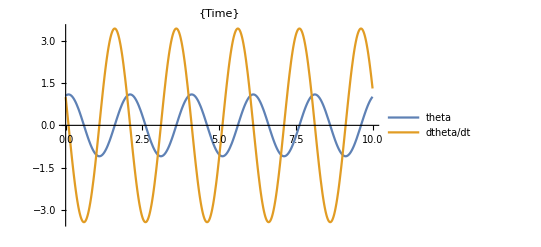

```mathematica
Plot[{theta, thetad}, {t, 0, 10}, PlotLegends->{"theta", "dtheta/dt"}, PlotLabel->{"Time"}]
```

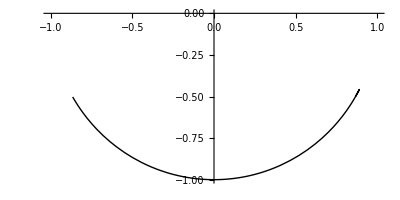

```mathematica
ParametricPlot[{1Sin[theta], -1Cos[theta]}, {t, 0, 1}, PlotRange->{{-1, 1}, {-1, 0}}, PlotStyle->{Thick, Black}]
```

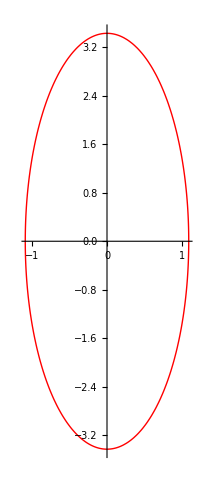

```mathematica
ParametricPlot[{theta, thetad}, {t, 0, 2Pi / wn}, PlotStyle->{Thick, Red}]
```

```mathematica
?Table
```

Table[expr,n] generates a list of n copies of expr. 
Table[expr,{i,i_max}] generates a list of the values of expr when i runs from 1 to i_max. 
Table[expr,{i,i_min,i_max}] starts with i=i_min. 
Table[expr,{i,i_min,i_max,di}] uses steps di. 
Table[expr,{i,{i_1,i_2,…}}] uses the successive values i_1, i_2, ….
Table[expr,{i,i_min,i_max},{j,j_min,j_max},…] gives a nested list. The list associated with i is outermost.

```mathematica
Table[{Cos[t], Sin[t]}, {t, 0, 2Pi, 0.1}]
```

{{1.,0.},{0.995004,0.0998334},{0.980067,0.198669},{0.955336,0.29552},{0.921061,0.389418},{0.877583,0.479426},{0.825336,0.564642},{0.764842,0.644218},{0.696707,0.717356},{0.62161,0.783327},{0.540302,0.841471},{0.453596,0.891207},{0.362358,0.932039},{0.267499,0.963558},{0.169967,0.98545},{0.0707372,0.997495},{-0.0291995,0.999574},{-0.128844,0.991665},{-0.227202,0.973848},{-0.32329,0.9463},{-0.416147,0.909297},{-0.504846,0.863209},{-0.588501,0.808496},{-0.666276,0.745705},{-0.737394,0.675463},{-0.801144,0.598472},{-0.856889,0.515501},{-0.904072,0.42738},{-0.942222,0.334988},{-0.970958,0.239249},{-0.989992,0.14112},{-0.999135,0.0415807},{-0.998295,-0.0583741},{-0.98748,-0.157746},{-0.966798,-0.255541},{-0.936457,-0.350783},{-0.896758,-0.44252},{-0.8481,-0.529836},{-0.790968,-0.611858},{-0.725932,-0.687766},{-0.653644,-0.756802},{-0.574824,-0.818277},{-0.490261,-0.871576},{-0.400799,-0.916166},{-0.307333,-0.951602},{-0.210796,-0.97753},{-0.112153,-0.993691},{-0.0123887,-0.999923},{0.087499,-0.996165},{0.186512,-0.982453},{0.283662,-0.958924},{0.377978,-0.925815},{0.468517,-0.883455},{0.554374,-0.832267},{0.634693,-0.772764},{0.70867,-0.70554},{0.775566,-0.631267},{0.834713,-0.550686},{0.88552,-0.464602},{0.927478,-0.373877},{0.96017,-0.279415},{0.983268,-0.182163},{0.996542,-0.0830894}}

```mathematica
?ListLinePlot
```

ListLinePlot[{y_1,y_2,…}] plots a line through the points {1,y_1},{2,y_2},….
ListLinePlot[{{x_1,y_1},{x_2,y_2},…}] plots a line through a list of points with specific x and y positions. 
ListLinePlot[{data_1,data_2,…}] plots data from all the data_i. 
ListLinePlot[{…,w[data_i,…],…}] plots data_i with features defined by the symbolic wrapper w.

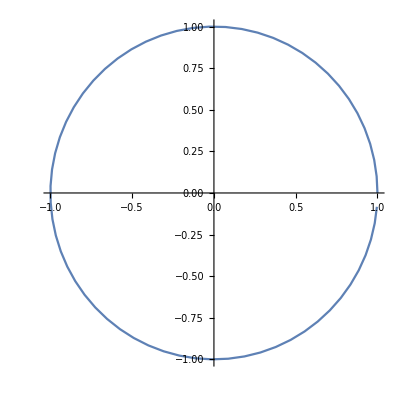

```mathematica
ListLinePlot[Table[{Cos[t], Sin[t]}, {t, 0, 2Pi, 0.1}], AspectRatio->1]
```

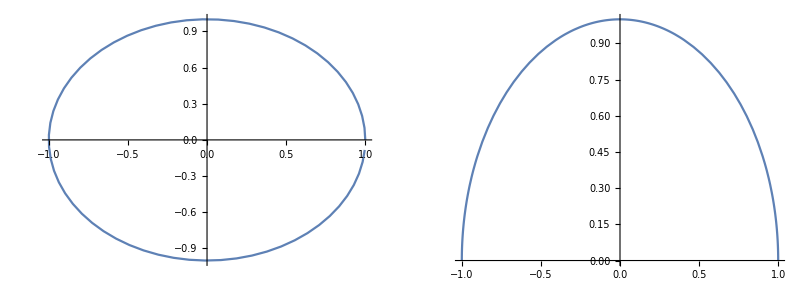

```mathematica
GraphicsRow[{ListLinePlot[Table[{Cos[t], Sin[t]}, {t, 0, 2Pi, 0.1}], AspectRatio->1],
ParametricPlot[{Cos[t], Sin[t]}, {t, 0, Pi}]}]
```

```mathematica
?GraphicsRow
```

GraphicsRow[{g_1,g_2,…}] generates a graphic in which the g_i are laid out in a row.
GraphicsRow[list,spacing] leaves the specified spacing between successive elements.

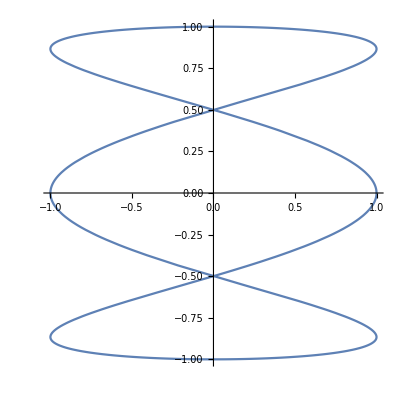

```mathematica
ParametricPlot[{Sin[3 t + Pi / 2], Sin[t]}, {t, 0, 2Pi}]
```

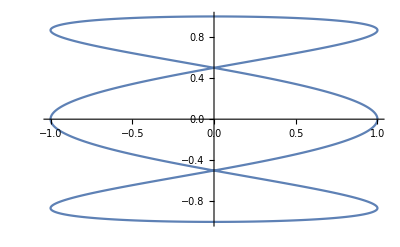

```mathematica
ListLinePlot[Table[{Sin[3 t + Pi / 2], Sin[t]}, {t, 0, 2Pi, 0.01}]]
```

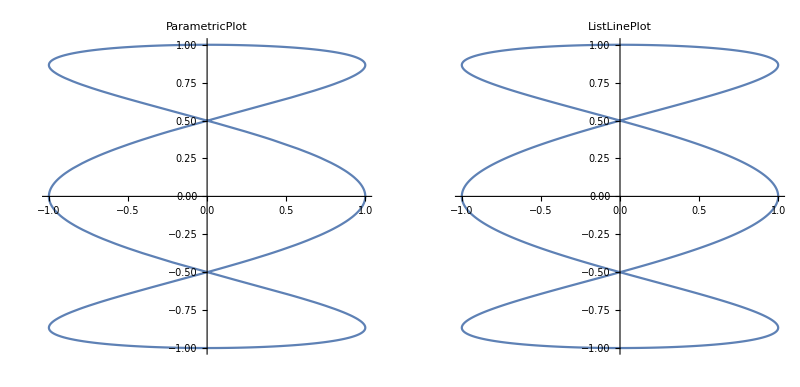

```mathematica
GraphicsRow[{
ParametricPlot[{Sin[3 t + Pi / 2], Sin[t]}, {t, 0, 2Pi}, PlotLabel->"ParametricPlot", AspectRatio->1],
ListLinePlot[Table[{Sin[3 t + Pi / 2], Sin[t]}, {t, 0, 2Pi, 0.01}], PlotLabel->"ListLinePlot", AspectRatio->1]
}]
```